## Tensor Manipulation

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.5, {2021,2,28}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;
(* evita que salgan los indices feos *)
$CommuteCovDsOnScalars=True;
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]
```

((▽_a φ^*) (▽^a φ))

```mathematica
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[Mp, PrintAs ->"Mp"];
DefConstantSymbol[L3, PrintAs ->"Λ"];
DefConstantSymbol[c4, PrintAs ->"c"];
DefConstantSymbol[d4, PrintAs ->"d"];
DefConstantSymbol[ka, PrintAs ->"k"]
```

```mathematica
(*Mp=1/Sqrt[8pi G]  -> h=c=1*)
```

```mathematica
L=Sqrt[-Detmetric[]]*(1/2 Mp^2 RicciScalarCD[]-ka(X[]+mS^2*PhiC[]*Phi[])+Mp/L3^3(c4 X[] RicciScalarCD[]-2 c4 (CD[-h]@CD[h]@Phi[]*CD[-f]@CD[f]@PhiC[]-CD[f]@CD[h]@Phi[]*CD[-f]@CD[-h]@PhiC[])+d4*1/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][PhiC[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][PhiC[]]])));
```

```mathematica
(*Horndeski*)
```

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation[L/.d4->0];
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=1/Sqrt[-Detmetric[]](VarD[PertPhiC[LI[1]],CD][Lpert]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification
```

(-k Λ^3 m^2 φ+(k Λ^3-c Mp R[▽]) (▽_a▽^a φ)-c Mp (▽_a R[▽]) (▽^a φ)+2 c Mp (▽_b▽_a▽^b▽^a φ)-2 c Mp (▽_b▽^b▽_a▽^a φ))/Λ^3

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//NoScalar//ReplaceDummies//ToCanonical //RicciToEinstein//ContractMetric//Simplification 
(*Collect[Ecuϕ,{c4,d4},Simplify]/.d4->0*)
```

-k m^2 φ+k (▽_a▽^a φ)+(2 c Mp G[▽] | a | b
  |   (▽_b▽_a φ))/Λ^3

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-2/Sqrt[-Detmetric[]] VarD[metpert[LI[1],a,b],CD][Lpert]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical; (* 2  it is because we defined  Subscript[T, μν]=-2/(√-g) δS/δg^μν *)
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical (*//RicciToEinstein//Simplification*);
```

```mathematica
Ecu=Collect[Ecu, {c4, L3},Simplify]
```

Mp^2 G[▽] |   |  
a | b+k (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (m^2 φ φ^*+(▽_c φ^*) (▽^c φ)))+1/Λ^3 c Mp ((▽_a φ^*) (R[▽] (▽_b φ)-2 R[▽] |   |  
b | c (▽^c φ))+(▽_a φ) (R[▽] (▽_b φ^*)-2 R[▽] |   |  
b | c (▽^c φ^*))+2 ((▽_b▽_a φ^*) (▽_c▽^c φ)+(▽_b▽_a φ) (▽_c▽^c φ^*)-R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)+G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)-R[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)-(▽_c▽_b φ^*) (▽^c▽_a φ)-(▽_c▽_a φ^*) (▽^c▽_b φ)-g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)+2 g |   |  
a | b R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)+g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)))

```mathematica
Trac=metric[a,b]Ecu//ContractMetric//ToCanonical
```

Mp^2 G[▽] | a |  
  | a+4 k m^2 φ φ^*+2 k (▽_a φ^*) (▽^a φ)+(2 c Mp G[▽] | b |  
  | b (▽_a φ^*) (▽^a φ))/Λ^3+(2 c Mp R[▽] (▽_a φ^*) (▽^a φ))/Λ^3-(4 c Mp (▽_a▽^a φ) (▽_b▽^b φ^*))/Λ^3+(4 c Mp R[▽] |   |  
a | b (▽^a φ) (▽^b φ^*))/Λ^3+(4 c Mp (▽_b▽_a φ^*) (▽^b▽^a φ))/Λ^3

```mathematica
pap=2{{G[▽], {{, }, {a, b}}}} X[]+2 {{g, {{, }, {a, b}}}}((▽_d▽_c SuperStar[φ]) (▽^d▽^c φ)-(▽_c▽^c φ) (▽_d▽^d SuperStar[φ])+2{{R[▽], {{, }, {c, d}}}} (▽^c φ) (▽^d SuperStar[φ]))-2({{R[▽], {{, , , }, {a, c, b, d}}}} +{{R[▽], {{, , , }, {a, d, b, c}}}} )(▽^c φ) (▽^d SuperStar[φ])+((▽_a φ) (R[▽] (▽_b SuperStar[φ])-2 {{R[▽], {{, }, {b, c}}}} (▽^c SuperStar[φ]))+2((▽_b▽_a SuperStar[φ]) (▽_c▽^c φ)-{{R[▽], {{, }, {a, c}}}} (▽_b SuperStar[φ]) (▽^c φ)-(▽_c▽_b SuperStar[φ]) (▽^c▽_a φ)))
```

2 G[▽] |   |  
a | b ((▽_a φ^*) (▽^a φ))+(▽_a φ) (R[▽] (▽_b φ^*)-2 R[▽] |   |  
b | c (▽^c φ^*))+2 ((▽_b▽_a φ^*) (▽_c▽^c φ)-R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)-(▽_c▽_b φ^*) (▽^c▽_a φ))-2 (R[▽] |   |   |   |  
a | c | b | d+R[▽] |   |   |   |  
a | d | b | c) (▽^c φ) (▽^d φ^*)+2 g |   |  
a | b (-(▽_c▽^c φ) (▽_d▽^d φ^*)+2 R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ))

```mathematica
(*Checking recovering EKG and GR*)
```

```mathematica
DefTensor[TT[a,b],M4,PrintAs->"TT"]
```

```mathematica
(*EKG*)
```

Note that we need to account for the definition of T_μν= -2/(√-g) δS/δg^μν in the equation.

```mathematica
EKG=Solve[(Ecu/.{c4-> 0})==TT[-a,-b],{{G[▽], {{, }, {a, b}}}}]
EKG[[1,1,1]]==Collect[EKG[[1,1,2]],{ka}]/.ka->1
EKG[[1,1,1]]==Collect[EKG[[1,1,2]],{ka}]/.ka->0
```

{{G[▽] |   |  
a | b→(-k m^2 g |   |  
a | b φ φ^*+TT |   |  
a | b+k (▽_a φ^*) (▽_b φ)+k (▽_a φ) (▽_b φ^*)-k g |   |  
a | b (▽_c φ^*) (▽^c φ))/Mp^2}}

G[▽] |   |  
a | b==(TT |   |  
a | b)/Mp^2+(-m^2 g |   |  
a | b φ φ^*+(▽_a φ^*) (▽_b φ)+(▽_a φ) (▽_b φ^*)-g |   |  
a | b (▽_c φ^*) (▽^c φ))/Mp^2

G[▽] |   |  
a | b==(TT |   |  
a | b)/Mp^2

```mathematica
(* G=1/Mp^2(Tab+Tϕ) *)
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

```mathematica
DefTensor[uu[a],M4,PrintAs->"u"]
DefTensor[T[a,b],M4,PrintAs->"T"]
```

```mathematica
Uup=CTensor[{-1/NN[r[]],0,0,0},{esf}]
Udown=CTensor[{ NN[r[]],0,0,0},{-esf}]
```

CTensor[{-1/NN[r],0,0,0},{esf},0]

CTensor[{NN[r],0,0,0},{-esf},0]

```mathematica
(*checking*)
```

```mathematica
ComponentValue[uu[b_],Uup[b]]
ComponentValue[uu[-b_],Udown[-b]]
```

u | b̲
 →-1/NN[r]
0
0
0 | b

u |  
b̲→NN[r]
0
0
0 |  
b

We can check this by raising the lower index or lowering the raised index:

```mathematica
metric[a,b]uu[-b]//ToBasis[esf]//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues
metric[-a,-b]uu[b]//ToBasis[esf]//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues
```

{-1/NN[r],0,0,0}

{NN[r],0,0,0}

And we can check the normalisation

```mathematica
metric[-a,-b]uu[a]uu[b]//ToBasis[esf]//ToBasis[esf]//TraceBasisDummy//ToValues//ToValues
```

-1

Defining the tensor of energy and momentum of perfect fluid

```mathematica
DefScalarFunction[den,PrintAs->"ρ"]
DefScalarFunction[pres,PrintAs->"P"]
DefConstantSymbol[epsil,PrintAs->"ϵ"]
```

```mathematica
IndexSet[T[a_,b_],(den[r[]](1+epsil)+pres[r[]])uu[a]uu[b]+pres[r[]]metric[a,b]]
```

g | a | b
  |   P[r]+((1+ϵ) ρ[r]+P[r]) u | a
  u | b

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]

ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
```

Computed ▽φ | a
 →▽φ |  
b g | a | b
  |   in 0.01452 Seconds

Computed ▽▽φ |   | b
a |  →▽▽φ |   |  
a | c g | b | c
  |   in 0.095576 Seconds

Computed ▽▽φ | a | b
  |  →▽▽φ |   | b
c |   g | a | c
  |   in 0.084851 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.380319 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.662413 Seconds

Computed ▽▽▽φ | a | b | c
  |   |  →▽▽▽φ |   | b | c
d |   |   g | a | d
  |   in 0.712226 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.869299 Seconds

Computed ▽▽▽φ | a | b |  
  |   | c→▽▽▽φ |   | b |  
d |   | c g | a | d
  |   in 0.617653 Seconds

Computed ▽▽▽φ | a |   |  
  | b | c→▽▽▽φ |   |   |  
d | b | c g | a | d
  |   in 0.464256 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.423815 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.415714 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.400777 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.464616 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.423553 Seconds

Computed ▽φ^* | a
 →▽φ^* |  
b g | a | b
  |   in 0.01217 Seconds

Computed ▽▽φ^* |   | b
a |  →▽▽φ^* |   |  
a | c g | b | c
  |   in 0.08075 Seconds

Computed ▽▽φ^* | a | b
  |  →▽▽φ^* |   | b
c |   g | a | c
  |   in 0.092462 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.35085 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.579769 Seconds

Computed ▽▽▽φ^* | a | b | c
  |   |  →▽▽▽φ^* |   | b | c
d |   |   g | a | d
  |   in 0.671076 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 0.804597 Seconds

Computed ▽▽▽φ^* | a | b |  
  |   | c→▽▽▽φ^* |   | b |  
d |   | c g | a | d
  |   in 0.596897 Seconds

Computed ▽▽▽φ^* | a |   |  
  | b | c→▽▽▽φ^* |   |   |  
d | b | c g | a | d
  |   in 0.460653 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.410057 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.40457 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.414488 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 0.457173 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.410072 Seconds

Computed ▽R[▽] | a
 →▽R[▽] |  
b g | a | b
  |   in 0.01385 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.2749 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.475795 Seconds

Computed ▽R[▽] | a | b | c
  |   |  →▽R[▽] |   | b | c
d |   |   g | a | d
  |   in 0.439084 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.691926 Seconds

Computed ▽R[▽] | a | b |  
  |   | c→▽R[▽] |   | b |  
d |   | c g | a | d
  |   in 0.527153 Seconds

Computed ▽R[▽] | a |   |  
  | b | c→▽R[▽] |   |   |  
d | b | c g | a | d
  |   in 0.436388 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.390069 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.402854 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.406443 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.420613 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.408439 Seconds

Computed R[▽] |   | b
a |  →g | b | c
  |   R[▽] |   |  
a | c in 0.12973 Seconds

Computed R[▽] | a | b
  |  →g | a | c
  |   R[▽] |   | b
c |   in 0.079029 Seconds

Computed G[▽] |   | b
a |  →G[▽] |   |  
a | c g | b | c
  |   in 0.099816 Seconds

Computed G[▽] | a | b
  |  →G[▽] |   | b
c |   g | a | c
  |   in 0.090451 Seconds

```mathematica
(* computing the conservations equations *)
```

```mathematica
val[expr_]:=ToValues@ToValues@ComponentArray@ToValues@TraceBasisDummy@ToBasis[esf]@Implode@expr
```

```mathematica
conserv=(CD[-a][T[a,b]]//ToBasis[esf]//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//Simplify)
```

{0,((1+ϵ) ρ[r] NN'[r]+P[r] NN'[r]+NN[r] P'[r])/(gg[r]^2 NN[r]),0,0}

```mathematica
Dp=Solve[conserv[[2]]==0,P'[r]][[1,1]]/.Rule->Equal//Simplify
```

P'[r]==-(((1+ϵ) ρ[r]+P[r]) NN'[r])/NN[r]

```mathematica
(*scalar field equation *)
```

```mathematica
Hesfϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

1/(Λ^3 gg[r]^5 NN[r]^2 r^2)ⅇ^(ⅈ w t) (gg[r]^5 (-k Λ^3 m^2 NN[r]^2 r^2+w^2 (-2 c Mp+k Λ^3 r^2)) ϕ[r]-6 c Mp NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]-gg[r]^2 gg'[r] (4 c Mp w^2 r ϕ[r]+NN[r]^2 (-2 c Mp+k Λ^3 r^2) ϕ'[r])+2 c Mp gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (2 c Mp w^2 ϕ[r]+NN[r] ((-2 c Mp+k Λ^3 r^2) NN'[r] ϕ'[r]+NN[r] (2 k Λ^3 r ϕ'[r]+(-2 c Mp+k Λ^3 r^2) ϕ''[r]))))

```mathematica
eqϕ=Collect[Hesfϕ*Λ^3 gg[r]^5 NN[r]^2 r^2 ⅇ^(-ⅈ w t),{c4,L3}, Simplify]
```

k Λ^3 gg[r]^2 r (gg[r]^3 (w^2-m^2 NN[r]^2) r ϕ[r]-NN[r]^2 r gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 w^2 r ϕ[r]+NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r]))+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))

```mathematica
(*Einstein equations*)
```

Remember, 
G_ab = 1/Mpl T_ab   ->  Hesf= T_ab

```mathematica
traza=Trac//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

-1/(Λ^3 gg[r]^5 NN[r]^4 r^2)2 (Λ^3 gg[r]^5 NN[r]^2 (k w^2 r^2 ϕ[r]^2+NN[r]^2 (Mp^2-2 k m^2 r^2 ϕ[r]^2))-6 c Mp NN[r]^3 r gg'[r] (2 NN[r]+r NN'[r]) ϕ'[r]^2+Mp gg[r]^2 NN[r] r gg'[r] (2 Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-4 c w^2 NN[r] r ϕ[r] ϕ'[r])-gg[r]^3 (-4 c Mp w^2 r^2 ϕ[r]^2 NN'[r]^2+Λ^3 NN[r]^4 (Mp^2+k r^2 ϕ'[r]^2)+Λ^3 Mp^2 NN[r]^3 r (2 NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] r ϕ[r] (2 ϕ[r] NN'[r]+4 r NN'[r] ϕ'[r]+r ϕ[r] NN''[r])-4 c Mp w^2 NN[r]^2 r (2 ϕ[r] ϕ'[r]+r ϕ'[r]^2+r ϕ[r] ϕ''[r]))+2 c Mp gg[r] NN[r]^3 ϕ'[r] (2 NN[r] (ϕ'[r]+2 r ϕ''[r])+r (r ϕ'[r] NN''[r]+2 NN'[r] (2 ϕ'[r]+r ϕ''[r]))))

```mathematica
Hesf=Ecu//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

{{1/(Λ^3 gg[r]^5 r^2)(gg[r]^5 (w^2 (2 c Mp-k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 (Mp^2-k m^2 r^2 ϕ[r]^2))+2 Mp gg[r]^2 r (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) gg'[r]-12 c Mp NN[r]^2 r gg'[r] ϕ'[r]^2-gg[r]^3 (2 c Mp w^2 ϕ[r]^2+NN[r]^2 (Λ^3 Mp^2+(-2 c Mp+k Λ^3 r^2) ϕ'[r]^2))+2 c Mp gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r])),0,0,0},{0,1/(Λ^3 gg[r]^2 NN[r]^3 r^2)(gg[r]^4 (w^2 NN[r] (2 c Mp-k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^3 (-Mp^2+k m^2 r^2 ϕ[r]^2))-6 c Mp NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 Λ^3 Mp^2 NN[r]^2 r NN'[r]+4 c Mp w^2 r ϕ[r]^2 NN'[r]-2 c Mp w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^3 (Λ^3 Mp^2+(2 c Mp-k Λ^3 r^2) ϕ'[r]^2))),0,0},{0,0,1/(Λ^3 gg[r]^5 NN[r]^4)r (k Λ^3 gg[r]^5 NN[r]^2 (-w^2+m^2 NN[r]^2) r ϕ[r]^2+6 c Mp NN[r]^3 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^2-Mp gg[r]^2 NN[r] gg'[r] (Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-2 c w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))-2 c Mp gg[r] NN[r]^3 ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-4 c Mp w^2 r ϕ[r]^2 NN'[r]^2+k Λ^3 NN[r]^4 r ϕ'[r]^2+Λ^3 Mp^2 NN[r]^3 (NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))-4 c Mp w^2 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))),0},{0,0,0,1/(Λ^3 gg[r]^5 NN[r]^4)r Sin[θ]^2 (k Λ^3 gg[r]^5 NN[r]^2 (-w^2+m^2 NN[r]^2) r ϕ[r]^2+6 c Mp NN[r]^3 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^2-Mp gg[r]^2 NN[r] gg'[r] (Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-2 c w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))-2 c Mp gg[r] NN[r]^3 ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-4 c Mp w^2 r ϕ[r]^2 NN'[r]^2+k Λ^3 NN[r]^4 r ϕ'[r]^2+Λ^3 Mp^2 NN[r]^3 (NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))-4 c Mp w^2 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r]))))}}

```mathematica
(*matter fluid tensor *)
```

```mathematica
tensor=T[-a,-b]//ToBasis[esf]//ToBasis[esf]//ComponentArray//ToValues//TraceBasisDummy//ToValues//ToValues//Simplify
```

{{(1+ϵ) ρ[r] NN[r]^2,0,0,0},{0,gg[r]^2 P[r],0,0},{0,0,P[r] r^2,0},{0,0,0,P[r] r^2 Sin[θ]^2}}

```mathematica
Traztensor=metric[a,b]T[-a,-b]//ToBasis[esf]//ToBasis[esf]//ComponentArray//ToValues//TraceBasisDummy//ToValues//ToValues//Simplify
```

-((1+ϵ) ρ[r])+3 P[r]

```mathematica
T00=tensor[[1]][[1]]
T11=tensor[[2]][[2]]
```

(1+ϵ) ρ[r] NN[r]^2

gg[r]^2 P[r]

trace

```mathematica
eqTr=traza==Traztensor
```

-1/(Λ^3 gg[r]^5 NN[r]^4 r^2)2 (Λ^3 gg[r]^5 NN[r]^2 (k w^2 r^2 ϕ[r]^2+NN[r]^2 (Mp^2-2 k m^2 r^2 ϕ[r]^2))-6 c Mp NN[r]^3 r gg'[r] (2 NN[r]+r NN'[r]) ϕ'[r]^2+Mp gg[r]^2 NN[r] r gg'[r] (2 Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-4 c w^2 NN[r] r ϕ[r] ϕ'[r])-gg[r]^3 (-4 c Mp w^2 r^2 ϕ[r]^2 NN'[r]^2+Λ^3 NN[r]^4 (Mp^2+k r^2 ϕ'[r]^2)+Λ^3 Mp^2 NN[r]^3 r (2 NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] r ϕ[r] (2 ϕ[r] NN'[r]+4 r NN'[r] ϕ'[r]+r ϕ[r] NN''[r])-4 c Mp w^2 NN[r]^2 r (2 ϕ[r] ϕ'[r]+r ϕ'[r]^2+r ϕ[r] ϕ''[r]))+2 c Mp gg[r] NN[r]^3 ϕ'[r] (2 NN[r] (ϕ'[r]+2 r ϕ''[r])+r (r ϕ'[r] NN''[r]+2 NN'[r] (2 ϕ'[r]+r ϕ''[r]))))==-((1+ϵ) ρ[r])+3 P[r]

The 00-11 equations are

```mathematica
Eq00=(Collect[Hesf[[1]][[1]],{c4,L3}, Simplify])==tensor[[1]][[1]]
```

(gg[r]^3 (-k w^2 r^2 ϕ[r]^2+NN[r]^2 (Mp^2-k m^2 r^2 ϕ[r]^2))+2 Mp^2 NN[r]^2 r gg'[r]-gg[r] NN[r]^2 (Mp^2+k r^2 ϕ'[r]^2))/(gg[r]^3 r^2)+(2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 w^2 gg[r]^2 r ϕ[r]^2 gg'[r]-6 NN[r]^2 r gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r])))/(Λ^3 gg[r]^5 r^2)==(1+ϵ) ρ[r] NN[r]^2

```mathematica
Eq11=(Collect[Hesf[[2]][[2]],{c4,L3}, Simplify])==tensor[[2]][[2]]
```

Mp^2/r^2+gg[r]^2 (-Mp^2/r^2+k (m^2-w^2/NN[r]^2) ϕ[r]^2)+(2 Mp^2 NN'[r])/(NN[r] r)-k ϕ'[r]^2+(2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 w^2 r ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r]))))/(Λ^3 gg[r]^2 NN[r]^3 r^2)==gg[r]^2 P[r]

```mathematica
(*checking: recovering the TOV equation*)
```

```mathematica
TOV0=Eq00/.{ka-> 0, c4-> 0,epsil-> 0 }
```

(-Mp^2 gg[r] NN[r]^2+Mp^2 gg[r]^3 NN[r]^2+2 Mp^2 NN[r]^2 r gg'[r])/(gg[r]^3 r^2)==ρ[r] NN[r]^2

```mathematica
TOV0=Collect[TOV0[[1]],{Mp,NN[r[]]},Expand]==TOV0[[2]]
```

Mp^2 NN[r]^2 (1/r^2-1/(gg[r]^2 r^2)+(2 gg'[r])/(gg[r]^3 r))==ρ[r] NN[r]^2

```mathematica
TOV1=Eq11/.{ka-> 0, c4-> 0,epsil-> 0 }
```

Mp^2/r^2-(Mp^2 gg[r]^2)/r^2+(2 Mp^2 NN'[r])/(NN[r] r)==gg[r]^2 P[r]

```mathematica
TOV1=Collect[TOV1[[1]],{Mp,r[]},Expand]==TOV1[[2]]
```

Mp^2 ((1-gg[r]^2)/r^2+(2 NN'[r])/(NN[r] r))==gg[r]^2 P[r]

### Solved the System of equation

```mathematica
(*con la traza*)
```

```mathematica
system=Last@Solve[{Eq00,Eq11,eqϕ==0,eqTr},{NN'[r], gg'[r],ϕ''[r],NN''[r]}]
```

{NN'[r]→-(NN[r] (-Λ^3 Mp^2 gg[r]^2 NN[r]^2+Λ^3 Mp^2 gg[r]^4 NN[r]^2+Λ^3 gg[r]^4 NN[r]^2 P[r] r^2+7+6 c Mp NN[r]^2 ϕ'[r]^2-2 c Mp gg[r]^2 NN[r]^2 ϕ'[r]^2+k Λ^3 gg[r]^2 NN[r]^2 r^2 ϕ'[r]^2))/(-2 Λ^3 Mp^2 gg[r]^2 NN[r]^2 r-4 c Mp w^2 gg[r]^2 r ϕ[r]^2+12 c Mp NN[r]^2 r ϕ'[r]^2),gg'[r]→-(gg[r] (1))/1,ϕ''[r]→1/(66+1),NN''[r]→1/(4 k Λ^18 Mp^7 gg[r]^10 NN[r]^10 r^4+141)}
 |  |  |  |

```mathematica
(*sin la traza*)
```

```mathematica
system=Last@Solve[{Eq00,Eq11,eqϕ==0},{NN'[r], gg'[r],ϕ''[r]}]//Simplify
```

{NN'[r]→(NN[r] (gg[r]^4 (w^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 (Mp^2+P[r] r^2-k m^2 r^2 ϕ[r]^2))+6 c Mp NN[r]^2 ϕ'[r]^2+gg[r]^2 (2 c Mp w^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-Λ^3 Mp^2+(-2 c Mp+k Λ^3 r^2) ϕ'[r]^2))))/(2 Mp r (gg[r]^2 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2)-6 c NN[r]^2 ϕ'[r]^2)),gg'[r]→(gg[r]^8 (4 c w^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 r^2 (k Λ^3 Mp+2 c P[r]-2 c k m^2 ϕ[r]^2)) (w^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 (-Mp^2+(1+ϵ) ρ[r] r^2+k m^2 r^2 ϕ[r]^2))+gg[r]^6 (-16 c^2 Mp w^4 (2 c Mp-k Λ^3 r^2) ϕ[r]^3 (ϕ[r]+2 r ϕ'[r])+2 c w^2 NN[r]^2 ϕ[r] (2 c k Λ^3 Mp m^2 r^2 ϕ[r]^3+4 Λ^3 Mp r (2 c (1+ϵ) ρ[r] r^2+Mp (-4 c Mp+k Λ^3 r^2)) ϕ'[r]+ϕ[r] (-8 c Λ^3 Mp^3+3 k Λ^6 Mp^2 r^2+4 c (1+ϵ) Λ^3 Mp ρ[r] r^2+2 c Λ^3 Mp P[r] r^2+8 c^2 Mp^2 ϕ'[r]^2-8 c k Λ^3 Mp r^2 ϕ'[r]^2+2 k^2 Λ^6 r^4 ϕ'[r]^2))+Λ^3 NN[r]^4 (k Λ^6 Mp^3 r^2-8 c k Λ^3 Mp^2 m^2 r^3 ϕ[r] ϕ'[r]-16 c^2 Mp^3 ϕ'[r]^2+6 c k Λ^3 Mp^2 r^2 ϕ'[r]^2+8 c^2 Mp ρ[r] r^2 ϕ'[r]^2+8 c^2 ϵ Mp ρ[r] r^2 ϕ'[r]^2+k^2 Λ^6 Mp r^4 ϕ'[r]^2-4 c k Λ^3 ρ[r] r^4 ϕ'[r]^2-4 c ϵ k Λ^3 ρ[r] r^4 ϕ'[r]^2+2 c k m^2 r^2 ϕ[r]^2 (-Λ^3 Mp^2+5 (2 c Mp-k Λ^3 r^2) ϕ'[r]^2)+2 c P[r] r^2 (Λ^3 Mp^2+(-6 c Mp+3 k Λ^3 r^2) ϕ'[r]^2)))+2 c Mp gg[r]^4 (8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])+Λ^3 NN[r]^4 ϕ'[r]^2 (20 c Mp^2+3 k Λ^3 Mp r^2+10 c P[r] r^2-10 c k m^2 r^2 ϕ[r]^2+24 c k m^2 r^3 ϕ[r] ϕ'[r])+4 c w^2 NN[r]^2 ϕ[r] (4 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (Λ^3 Mp^2+(-6 c Mp+7 k Λ^3 r^2) ϕ'[r]^2)))+48 c^3 Mp^2 NN[r]^3 ϕ'[r]^4 (3 NN[r]-4 r^2 NN''[r])-8 c^2 Mp gg[r]^2 NN[r] ϕ'[r]^2 (-4 c Mp w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r])+NN[r]^3 (3 Λ^3 Mp^2+(14 c Mp+5 k Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 NN[r]^2 r^2 NN''[r]-8 c Mp w^2 r^2 ϕ[r]^2 NN''[r]))/(2 Mp gg[r] r (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c w^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 r^2 (k Λ^3 Mp+2 c P[r]-2 c k m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+NN[r]^2 (-2 c Mp+k Λ^3 r^2) ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+k Λ^3 Mp r^2-2 c P[r] r^2+2 c k m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])))),ϕ''[r]→(gg[r]^8 (2 c w^4 NN[r] ϕ[r]^3 (-2 k Λ^6 Mp^2 r^3+4 c (1+ϵ) Λ^3 Mp ρ[r] r^3+8 c k Λ^3 Mp m^2 r^3 ϕ[r]^2+3 (-2 c Mp+k Λ^3 r^2)^2 ϕ[r] ϕ'[r])+Λ^6 NN[r]^5 (2 k Λ^3 Mp^3 m^2 r^3 ϕ[r]+((1+ϵ) ρ[r] r^2 (6 c P[r] r^2+Mp (4 c Mp+k Λ^3 r^2))-Mp (2 Mp^2 (c Mp+k Λ^3 r^2)+P[r] (4 c Mp r^2+k Λ^3 r^4))) ϕ'[r]+2 k m^2 r^2 (4 c Mp^2+k Λ^3 Mp r^2-3 c (1+ϵ) ρ[r] r^2+3 c P[r] r^2) ϕ[r]^2 ϕ'[r]-6 c k^2 m^4 r^4 ϕ[r]^4 ϕ'[r])+2 Λ^3 w^2 NN[r]^3 ϕ[r] (-k Λ^6 Mp^3 r^3+6 c k Λ^3 Mp^2 m^2 r^3 ϕ[r]^2+2 c (2 c Mp-k Λ^3 r^2) (Mp^2-P[r] r^2) ϕ[r] ϕ'[r]+2 c k m^2 r^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^3 ϕ'[r]+2 c (1+ϵ) ρ[r] r^2 (Λ^3 Mp^2 r+2 (-2 c Mp+k Λ^3 r^2) ϕ[r] ϕ'[r])))+2 gg[r]^6 NN[r] ϕ'[r] (4 c^2 Mp w^4 ϕ[r]^3 ((-6 c Mp+k Λ^3 r^2) ϕ[r]+8 r (-2 c Mp+k Λ^3 r^2) ϕ'[r])-Λ^3 NN[r]^4 (Λ^3 Mp^3 (2 c Mp+k Λ^3 r^2)+12 c k Λ^3 Mp^2 m^2 r^3 ϕ[r] ϕ'[r]+6 c (2 c Mp-k Λ^3 r^2) (Mp^2+P[r] r^2) ϕ'[r]^2+6 c k m^2 r^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2 ϕ'[r]^2)+2 c w^2 NN[r]^2 ϕ[r] (6 c k Λ^3 Mp m^2 r^2 ϕ[r]^3+Λ^3 Mp r (6 c (1+ϵ) ρ[r] r^2+Mp (-16 c Mp+5 k Λ^3 r^2)) ϕ'[r]-6 c k Λ^3 Mp m^2 r^3 ϕ[r]^2 ϕ'[r]+ϕ[r] (6 c (1+ϵ) Λ^3 Mp ρ[r] r^2-Λ^3 Mp^2 (8 c Mp+3 k Λ^3 r^2)+3 (-2 c Mp+k Λ^3 r^2)^2 ϕ'[r]^2)))+72 c^3 Mp^2 NN[r]^4 ϕ'[r]^5 (3 NN[r]-4 r^2 NN''[r])-24 c^2 Mp gg[r]^2 NN[r]^2 ϕ'[r]^3 (2 c Mp w^2 NN[r] ϕ[r] (ϕ[r]-2 r ϕ'[r])+3 NN[r]^3 (Λ^3 Mp^2+(2 c Mp+k Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 NN[r]^2 r^2 NN''[r]-8 c Mp w^2 r^2 ϕ[r]^2 NN''[r])+2 c gg[r]^4 ϕ'[r] (4 c^2 Mp^2 w^4 NN[r] ϕ[r]^3 (3 ϕ[r]+4 r ϕ'[r])+NN[r]^5 (3 Λ^6 Mp^4+2 Λ^3 Mp (16 c Mp^2+7 k Λ^3 Mp r^2+6 c P[r] r^2-6 c k m^2 r^2 ϕ[r]^2) ϕ'[r]^2+36 c k Λ^3 Mp m^2 r^3 ϕ[r] ϕ'[r]^3+3 (-2 c Mp+k Λ^3 r^2)^2 ϕ'[r]^4)+4 c Mp w^2 NN[r]^3 ϕ[r] (2 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (3 Λ^3 Mp^2-8 (c Mp-2 k Λ^3 r^2) ϕ'[r]^2))-4 Λ^6 Mp^4 NN[r]^4 r^2 NN''[r]-16 c Λ^3 Mp^3 w^2 NN[r]^2 r^2 ϕ[r]^2 NN''[r]-16 c^2 Mp^2 w^4 r^2 ϕ[r]^4 NN''[r]))/(2 Mp gg[r]^2 NN[r] r (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c w^2 (-2 c Mp+k Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 r^2 (k Λ^3 Mp+2 c P[r]-2 c k m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+NN[r]^2 (-2 c Mp+k Λ^3 r^2) ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+k Λ^3 Mp r^2-2 c P[r] r^2+2 c k m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))))}

```mathematica
DN=system[[1]]/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}/.Rule-> Equal
```

NN'[r]==(NN[r] (gg[r]^4 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp^2+r^2 P[r]-m^2 r^2 ϕ[r]^2))+6 c Mp NN[r]^2 ϕ'[r]^2+gg[r]^2 (2 c Mp w^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-Λ^3 Mp^2+(-2 c Mp+Λ^3 r^2) ϕ'[r]^2))))/(2 Mp r (gg[r]^2 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2)-6 c NN[r]^2 ϕ'[r]^2))

```mathematica
Dg=system[[2]]/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}/.Rule-> Equal
```

gg'[r]==(gg[r]^8 (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2)) ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (-Mp^2+r^2 (1+ϵ) ρ[r]+m^2 r^2 ϕ[r]^2))+gg[r]^6 (-16 c^2 Mp (2 c Mp-Λ^3 r^2) w^4 ϕ[r]^3 (ϕ[r]+2 r ϕ'[r])+2 c w^2 NN[r]^2 ϕ[r] (2 c Λ^3 m^2 Mp r^2 ϕ[r]^3+4 Λ^3 Mp r (Mp (-4 c Mp+Λ^3 r^2)+2 c r^2 (1+ϵ) ρ[r]) ϕ'[r]+ϕ[r] (-8 c Λ^3 Mp^3+3 Λ^6 Mp^2 r^2+4 c Λ^3 Mp r^2 (1+ϵ) ρ[r]+2 c Λ^3 Mp r^2 P[r]+8 c^2 Mp^2 ϕ'[r]^2-8 c Λ^3 Mp r^2 ϕ'[r]^2+2 Λ^6 r^4 ϕ'[r]^2))+Λ^3 NN[r]^4 (Λ^6 Mp^3 r^2-8 c Λ^3 m^2 Mp^2 r^3 ϕ[r] ϕ'[r]-16 c^2 Mp^3 ϕ'[r]^2+6 c Λ^3 Mp^2 r^2 ϕ'[r]^2+Λ^6 Mp r^4 ϕ'[r]^2+8 c^2 Mp r^2 ρ[r] ϕ'[r]^2-4 c Λ^3 r^4 ρ[r] ϕ'[r]^2+8 c^2 Mp r^2 ϵ ρ[r] ϕ'[r]^2-4 c Λ^3 r^4 ϵ ρ[r] ϕ'[r]^2+2 c m^2 r^2 ϕ[r]^2 (-Λ^3 Mp^2+5 (2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 c r^2 P[r] (Λ^3 Mp^2+(-6 c Mp+3 Λ^3 r^2) ϕ'[r]^2)))+2 c Mp gg[r]^4 (8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])+Λ^3 NN[r]^4 ϕ'[r]^2 (20 c Mp^2+3 Λ^3 Mp r^2+10 c r^2 P[r]-10 c m^2 r^2 ϕ[r]^2+24 c m^2 r^3 ϕ[r] ϕ'[r])+4 c w^2 NN[r]^2 ϕ[r] (4 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (Λ^3 Mp^2+(-6 c Mp+7 Λ^3 r^2) ϕ'[r]^2)))+48 c^3 Mp^2 NN[r]^3 ϕ'[r]^4 (3 NN[r]-4 r^2 NN''[r])-8 c^2 Mp gg[r]^2 NN[r] ϕ'[r]^2 (-4 c Mp w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r])+NN[r]^3 (3 Λ^3 Mp^2+(14 c Mp+5 Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 r^2 NN[r]^2 NN''[r]-8 c Mp r^2 w^2 ϕ[r]^2 NN''[r]))/(2 Mp r gg[r] (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+Λ^3 Mp r^2-2 c r^2 P[r]+2 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))))

```mathematica
Ddϕ=system[[3]]/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}/.Rule-> Equal
```

ϕ''[r]==(gg[r]^8 (2 c w^4 NN[r] ϕ[r]^3 (-2 Λ^6 Mp^2 r^3+4 c Λ^3 Mp r^3 (1+ϵ) ρ[r]+8 c Λ^3 m^2 Mp r^3 ϕ[r]^2+3 (-2 c Mp+Λ^3 r^2)^2 ϕ[r] ϕ'[r])+Λ^6 NN[r]^5 (2 Λ^3 m^2 Mp^3 r^3 ϕ[r]+(r^2 (1+ϵ) ρ[r] (Mp (4 c Mp+Λ^3 r^2)+6 c r^2 P[r])-Mp (2 Mp^2 (c Mp+Λ^3 r^2)+(4 c Mp r^2+Λ^3 r^4) P[r])) ϕ'[r]+2 m^2 r^2 (4 c Mp^2+Λ^3 Mp r^2-3 c r^2 (1+ϵ) ρ[r]+3 c r^2 P[r]) ϕ[r]^2 ϕ'[r]-6 c m^4 r^4 ϕ[r]^4 ϕ'[r])+2 Λ^3 w^2 NN[r]^3 ϕ[r] (-Λ^6 Mp^3 r^3+6 c Λ^3 m^2 Mp^2 r^3 ϕ[r]^2+2 c (2 c Mp-Λ^3 r^2) (Mp^2-r^2 P[r]) ϕ[r] ϕ'[r]+2 c m^2 r^2 (-2 c Mp+Λ^3 r^2) ϕ[r]^3 ϕ'[r]+2 c r^2 (1+ϵ) ρ[r] (Λ^3 Mp^2 r+2 (-2 c Mp+Λ^3 r^2) ϕ[r] ϕ'[r])))+2 gg[r]^6 NN[r] ϕ'[r] (4 c^2 Mp w^4 ϕ[r]^3 ((-6 c Mp+Λ^3 r^2) ϕ[r]+8 r (-2 c Mp+Λ^3 r^2) ϕ'[r])-Λ^3 NN[r]^4 (Λ^3 Mp^3 (2 c Mp+Λ^3 r^2)+12 c Λ^3 m^2 Mp^2 r^3 ϕ[r] ϕ'[r]+6 c (2 c Mp-Λ^3 r^2) (Mp^2+r^2 P[r]) ϕ'[r]^2+6 c m^2 r^2 (-2 c Mp+Λ^3 r^2) ϕ[r]^2 ϕ'[r]^2)+2 c w^2 NN[r]^2 ϕ[r] (6 c Λ^3 m^2 Mp r^2 ϕ[r]^3+Λ^3 Mp r (Mp (-16 c Mp+5 Λ^3 r^2)+6 c r^2 (1+ϵ) ρ[r]) ϕ'[r]-6 c Λ^3 m^2 Mp r^3 ϕ[r]^2 ϕ'[r]+ϕ[r] (-Λ^3 Mp^2 (8 c Mp+3 Λ^3 r^2)+6 c Λ^3 Mp r^2 (1+ϵ) ρ[r]+3 (-2 c Mp+Λ^3 r^2)^2 ϕ'[r]^2)))+72 c^3 Mp^2 NN[r]^4 ϕ'[r]^5 (3 NN[r]-4 r^2 NN''[r])-24 c^2 Mp gg[r]^2 NN[r]^2 ϕ'[r]^3 (2 c Mp w^2 NN[r] ϕ[r] (ϕ[r]-2 r ϕ'[r])+3 NN[r]^3 (Λ^3 Mp^2+(2 c Mp+Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 r^2 NN[r]^2 NN''[r]-8 c Mp r^2 w^2 ϕ[r]^2 NN''[r])+2 c gg[r]^4 ϕ'[r] (4 c^2 Mp^2 w^4 NN[r] ϕ[r]^3 (3 ϕ[r]+4 r ϕ'[r])+NN[r]^5 (3 Λ^6 Mp^4+2 Λ^3 Mp (16 c Mp^2+7 Λ^3 Mp r^2+6 c r^2 P[r]-6 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+36 c Λ^3 m^2 Mp r^3 ϕ[r] ϕ'[r]^3+3 (-2 c Mp+Λ^3 r^2)^2 ϕ'[r]^4)+4 c Mp w^2 NN[r]^3 ϕ[r] (2 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (3 Λ^3 Mp^2-8 (c Mp-2 Λ^3 r^2) ϕ'[r]^2))-4 Λ^6 Mp^4 r^2 NN[r]^4 NN''[r]-16 c Λ^3 Mp^3 r^2 w^2 NN[r]^2 ϕ[r]^2 NN''[r]-16 c^2 Mp^2 r^2 w^4 ϕ[r]^4 NN''[r]))/(2 Mp r gg[r]^2 NN[r] (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+Λ^3 Mp r^2-2 c r^2 P[r]+2 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))))

```mathematica
dp=Dp/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}/.Rule-> Equal
```

P'[r]==-(((1+ϵ) ρ[r]+P[r]) NN'[r])/NN[r]

```mathematica
system2={Eq00,Eq11,eqϕ==0}/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}
```

{(gg[r]^3 (-r^2 w^2 ϕ[r]^2+NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp^2 r NN[r]^2 gg'[r]-gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))/(r^2 gg[r]^3)+(2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r])))/(Λ^3 r^2 gg[r]^5)==(1+ϵ) ρ[r] NN[r]^2,Mp^2/r^2+gg[r]^2 (-Mp^2/r^2+(m^2-w^2/NN[r]^2) ϕ[r]^2)+(2 Mp^2 NN'[r])/(r NN[r])-ϕ'[r]^2+(2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r]))))/(Λ^3 r^2 gg[r]^2 NN[r]^3)==gg[r]^2 P[r],Λ^3 r gg[r]^2 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 ϕ[r]+NN[r]^2 ϕ'[r])+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))==0}

```mathematica
Cons=conserv/.{r[]-> r, mS-> m,ka->1, epsil-> ϵ}
```

{0,((1+ϵ) ρ[r] NN'[r]+P[r] NN'[r]+NN[r] P'[r])/(gg[r]^2 NN[r]),0,0}

## Numerical Solutions

```mathematica
Quit[]
```

```mathematica
(* equations without separate *)
```

```mathematica
system2={(gg[r]^3 (-r^2 w^2 ϕ[r]^2+NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp^2 r NN[r]^2 gg'[r]-gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))/(r^2 gg[r]^3)+(2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r])))/(Λ^3 r^2 gg[r]^5)==(1+ϵ) ρ[r] NN[r]^2,Mp^2/r^2+gg[r]^2 (-Mp^2/r^2+(m^2-w^2/NN[r]^2) ϕ[r]^2)+(2 Mp^2 NN'[r])/(r NN[r])-ϕ'[r]^2+(2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r]))))/(Λ^3 r^2 gg[r]^2 NN[r]^3)==gg[r]^2 P[r],Λ^3 r gg[r]^2 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 ϕ[r]+NN[r]^2 ϕ'[r])+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))==0,((1+ϵ) ρ[r] NN'[r]+P[r] NN'[r]+NN[r] P'[r])/(gg[r]^2 NN[r])==0};
```

```mathematica
(* equations *)
```

```mathematica
DN=NN'[r]==(NN[r] (gg[r]^4 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp^2+r^2 P[r]-m^2 r^2 ϕ[r]^2))+6 c Mp NN[r]^2 ϕ'[r]^2+gg[r]^2 (2 c Mp w^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-Λ^3 Mp^2+(-2 c Mp+Λ^3 r^2) ϕ'[r]^2))))/(2 Mp r (gg[r]^2 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2)-6 c NN[r]^2 ϕ'[r]^2));
Dg=gg'[r]==(gg[r]^8 (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2)) ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (-Mp^2+r^2 (1+ϵ) ρ[r]+m^2 r^2 ϕ[r]^2))+gg[r]^6 (-16 c^2 Mp (2 c Mp-Λ^3 r^2) w^4 ϕ[r]^3 (ϕ[r]+2 r ϕ'[r])+2 c w^2 NN[r]^2 ϕ[r] (2 c Λ^3 m^2 Mp r^2 ϕ[r]^3+4 Λ^3 Mp r (Mp (-4 c Mp+Λ^3 r^2)+2 c r^2 (1+ϵ) ρ[r]) ϕ'[r]+ϕ[r] (-8 c Λ^3 Mp^3+3 Λ^6 Mp^2 r^2+4 c Λ^3 Mp r^2 (1+ϵ) ρ[r]+2 c Λ^3 Mp r^2 P[r]+8 c^2 Mp^2 ϕ'[r]^2-8 c Λ^3 Mp r^2 ϕ'[r]^2+2 Λ^6 r^4 ϕ'[r]^2))+Λ^3 NN[r]^4 (Λ^6 Mp^3 r^2-8 c Λ^3 m^2 Mp^2 r^3 ϕ[r] ϕ'[r]-16 c^2 Mp^3 ϕ'[r]^2+6 c Λ^3 Mp^2 r^2 ϕ'[r]^2+Λ^6 Mp r^4 ϕ'[r]^2+8 c^2 Mp r^2 ρ[r] ϕ'[r]^2-4 c Λ^3 r^4 ρ[r] ϕ'[r]^2+8 c^2 Mp r^2 ϵ ρ[r] ϕ'[r]^2-4 c Λ^3 r^4 ϵ ρ[r] ϕ'[r]^2+2 c m^2 r^2 ϕ[r]^2 (-Λ^3 Mp^2+5 (2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 c r^2 P[r] (Λ^3 Mp^2+(-6 c Mp+3 Λ^3 r^2) ϕ'[r]^2)))+2 c Mp gg[r]^4 (8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])+Λ^3 NN[r]^4 ϕ'[r]^2 (20 c Mp^2+3 Λ^3 Mp r^2+10 c r^2 P[r]-10 c m^2 r^2 ϕ[r]^2+24 c m^2 r^3 ϕ[r] ϕ'[r])+4 c w^2 NN[r]^2 ϕ[r] (4 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (Λ^3 Mp^2+(-6 c Mp+7 Λ^3 r^2) ϕ'[r]^2)))+48 c^3 Mp^2 NN[r]^3 ϕ'[r]^4 (3 NN[r]-4 r^2 NN''[r])-8 c^2 Mp gg[r]^2 NN[r] ϕ'[r]^2 (-4 c Mp w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r])+NN[r]^3 (3 Λ^3 Mp^2+(14 c Mp+5 Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 r^2 NN[r]^2 NN''[r]-8 c Mp r^2 w^2 ϕ[r]^2 NN''[r]))/(2 Mp r gg[r] (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+Λ^3 Mp r^2-2 c r^2 P[r]+2 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))));

Ddϕ=ϕ''[r]==(gg[r]^8 (2 c w^4 NN[r] ϕ[r]^3 (-2 Λ^6 Mp^2 r^3+4 c Λ^3 Mp r^3 (1+ϵ) ρ[r]+8 c Λ^3 m^2 Mp r^3 ϕ[r]^2+3 (-2 c Mp+Λ^3 r^2)^2 ϕ[r] ϕ'[r])+Λ^6 NN[r]^5 (2 Λ^3 m^2 Mp^3 r^3 ϕ[r]+(r^2 (1+ϵ) ρ[r] (Mp (4 c Mp+Λ^3 r^2)+6 c r^2 P[r])-Mp (2 Mp^2 (c Mp+Λ^3 r^2)+(4 c Mp r^2+Λ^3 r^4) P[r])) ϕ'[r]+2 m^2 r^2 (4 c Mp^2+Λ^3 Mp r^2-3 c r^2 (1+ϵ) ρ[r]+3 c r^2 P[r]) ϕ[r]^2 ϕ'[r]-6 c m^4 r^4 ϕ[r]^4 ϕ'[r])+2 Λ^3 w^2 NN[r]^3 ϕ[r] (-Λ^6 Mp^3 r^3+6 c Λ^3 m^2 Mp^2 r^3 ϕ[r]^2+2 c (2 c Mp-Λ^3 r^2) (Mp^2-r^2 P[r]) ϕ[r] ϕ'[r]+2 c m^2 r^2 (-2 c Mp+Λ^3 r^2) ϕ[r]^3 ϕ'[r]+2 c r^2 (1+ϵ) ρ[r] (Λ^3 Mp^2 r+2 (-2 c Mp+Λ^3 r^2) ϕ[r] ϕ'[r])))+2 gg[r]^6 NN[r] ϕ'[r] (4 c^2 Mp w^4 ϕ[r]^3 ((-6 c Mp+Λ^3 r^2) ϕ[r]+8 r (-2 c Mp+Λ^3 r^2) ϕ'[r])-Λ^3 NN[r]^4 (Λ^3 Mp^3 (2 c Mp+Λ^3 r^2)+12 c Λ^3 m^2 Mp^2 r^3 ϕ[r] ϕ'[r]+6 c (2 c Mp-Λ^3 r^2) (Mp^2+r^2 P[r]) ϕ'[r]^2+6 c m^2 r^2 (-2 c Mp+Λ^3 r^2) ϕ[r]^2 ϕ'[r]^2)+2 c w^2 NN[r]^2 ϕ[r] (6 c Λ^3 m^2 Mp r^2 ϕ[r]^3+Λ^3 Mp r (Mp (-16 c Mp+5 Λ^3 r^2)+6 c r^2 (1+ϵ) ρ[r]) ϕ'[r]-6 c Λ^3 m^2 Mp r^3 ϕ[r]^2 ϕ'[r]+ϕ[r] (-Λ^3 Mp^2 (8 c Mp+3 Λ^3 r^2)+6 c Λ^3 Mp r^2 (1+ϵ) ρ[r]+3 (-2 c Mp+Λ^3 r^2)^2 ϕ'[r]^2)))+72 c^3 Mp^2 NN[r]^4 ϕ'[r]^5 (3 NN[r]-4 r^2 NN''[r])-24 c^2 Mp gg[r]^2 NN[r]^2 ϕ'[r]^3 (2 c Mp w^2 NN[r] ϕ[r] (ϕ[r]-2 r ϕ'[r])+3 NN[r]^3 (Λ^3 Mp^2+(2 c Mp+Λ^3 r^2) ϕ'[r]^2)-4 Λ^3 Mp^2 r^2 NN[r]^2 NN''[r]-8 c Mp r^2 w^2 ϕ[r]^2 NN''[r])+2 c gg[r]^4 ϕ'[r] (4 c^2 Mp^2 w^4 NN[r] ϕ[r]^3 (3 ϕ[r]+4 r ϕ'[r])+NN[r]^5 (3 Λ^6 Mp^4+2 Λ^3 Mp (16 c Mp^2+7 Λ^3 Mp r^2+6 c r^2 P[r]-6 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+36 c Λ^3 m^2 Mp r^3 ϕ[r] ϕ'[r]^3+3 (-2 c Mp+Λ^3 r^2)^2 ϕ'[r]^4)+4 c Mp w^2 NN[r]^3 ϕ[r] (2 Λ^3 Mp^2 r ϕ'[r]+ϕ[r] (3 Λ^3 Mp^2-8 (c Mp-2 Λ^3 r^2) ϕ'[r]^2))-4 Λ^6 Mp^4 r^2 NN[r]^4 NN''[r]-16 c Λ^3 Mp^3 r^2 w^2 NN[r]^2 ϕ[r]^2 NN''[r]-16 c^2 Mp^2 r^2 w^4 ϕ[r]^4 NN''[r]))/(2 Mp r gg[r]^2 NN[r] (gg[r]^4 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) (4 c (-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 r^2 NN[r]^2 (Λ^3 Mp+2 c P[r]-2 c m^2 ϕ[r]^2))+24 c^2 NN[r]^2 ϕ'[r]^2 (2 c Mp w^2 ϕ[r]^2+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r]^2)+2 c gg[r]^2 (-3 Λ^3 NN[r]^4 (-4 c Mp^2+Λ^3 Mp r^2-2 c r^2 P[r]+2 c m^2 r^2 ϕ[r]^2) ϕ'[r]^2+4 c Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+8 c^2 Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))));

dp=P'[r]==-(((1+ϵ) ρ[r]+P[r]) NN'[r])/NN[r];
```

### Introducing the dimensionless variables

```mathematica
newVar={r-> x/m,pres[r]->m^2 Mp^2 P,den[r]->m^2 Mp^2 ρ,w-> ω m, ϕ[r]-> σ[x] Mp,ϕ'[r]->  D[σ[x],x]m Mp,ϕ''[r]-> D[σ[x],{x,2}] m^2 Mp,NN[r]-> NN[x],NN'[r]-> D[NN[x],x]m, NN''[r]-> D[NN[x],{x,2}] m^2,gg[r]-> gg[x],gg'[r]-> gg'[x]m,L3-> Λ Mp^(1/3)m^(2/3)};
```

```mathematica
(*N'*)
```

```mathematica
mdN=DN[[2]]/m/.newVar//Simplify
```

(NN[x] (gg[x]^4 ((-2 c4+x^2 Λ^3) ω^2 σ[x]^2+Λ^3 NN[x]^2 (1+P x^2-x^2 σ[x]^2))+6 c4 NN[x]^2 σ'[x]^2+gg[x]^2 (2 c4 ω^2 σ[x] (σ[x]+4 x σ'[x])+NN[x]^2 (-Λ^3+(-2 c4+x^2 Λ^3) σ'[x]^2))))/(2 x (gg[x]^2 (Λ^3 NN[x]^2+2 c4 ω^2 σ[x]^2)-6 c4 NN[x]^2 σ'[x]^2))

```mathematica
mdNU=DN[[2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]}
```

(NN[x] (gg[x]^4 ((-2 c4+x^2 Λ^3) ω^2 σ[x]^2+Λ^3 NN[x]^2 (1+P x^2-x^2 σ[x]^2))+6 c4 NN[x]^2 σ'[x]^2+gg[x]^2 (2 c4 ω^2 σ[x] (σ[x]+4 x σ'[x])+NN[x]^2 (-Λ^3+(-2 c4+x^2 Λ^3) σ'[x]^2))))/(2 x (gg[x]^2 (Λ^3 NN[x]^2+2 c4 ω^2 σ[x]^2)-6 c4 NN[x]^2 σ'[x]^2))

```mathematica
mdNU-mdN//Simplify
```

0

```mathematica
(*g'*)
```

```mathematica
mdg=Dg[[2]]/m/.newVar//Simplify
```

(gg[x]^8 (4 c4 (-2 c4+x^2 Λ^3) ω^2 σ[x]^2+x^2 Λ^3 NN[x]^2 (2 c4 P+Λ^3-2 c4 σ[x]^2)) ((-2 c4+x^2 Λ^3) ω^2 σ[x]^2+Λ^3 NN[x]^2 (-1+x^2 (1+ϵ) ρ+x^2 σ[x]^2))+gg[x]^6 (-16 c4^2 (2 c4-x^2 Λ^3) ω^4 σ[x]^3 (σ[x]+2 x σ'[x])+Λ^3 NN[x]^4 (x^2 Λ^3 (2 c4 P+Λ^3)-8 c4 x^3 Λ^3 σ[x] σ'[x]-(2 c4-x^2 Λ^3) (x^2 Λ^3+c4 (8+6 P x^2-4 x^2 (1+ϵ) ρ)) σ'[x]^2+2 c4 x^2 σ[x]^2 (-Λ^3+5 (2 c4-x^2 Λ^3) σ'[x]^2))+2 c4 ω^2 NN[x]^2 σ[x] (2 c4 x^2 Λ^3 σ[x]^3+4 x Λ^3 (x^2 Λ^3+2 c4 (-2+x^2 (1+ϵ) ρ)) σ'[x]+σ[x] (3 x^2 Λ^6+2 c4 Λ^3 (-4+P x^2+2 x^2 (1+ϵ) ρ)+2 (-2 c4+x^2 Λ^3)^2 σ'[x]^2)))+2 c4 gg[x]^4 (8 c4^2 ω^4 σ[x]^3 (σ[x]+4 x σ'[x])+Λ^3 NN[x]^4 σ'[x]^2 (10 c4 (2+P x^2)+3 x^2 Λ^3-10 c4 x^2 σ[x]^2+24 c4 x^3 σ[x] σ'[x])+4 c4 ω^2 NN[x]^2 σ[x] (4 x Λ^3 σ'[x]+σ[x] (Λ^3+(-6 c4+7 x^2 Λ^3) σ'[x]^2)))+48 c4^3 NN[x]^3 σ'[x]^4 (3 NN[x]-4 x^2 NN''[x])-8 c4^2 gg[x]^2 NN[x] σ'[x]^2 (-4 c4 ω^2 NN[x] σ[x] (σ[x]+2 x σ'[x])+NN[x]^3 (3 Λ^3+(14 c4+5 x^2 Λ^3) σ'[x]^2)-4 x^2 Λ^3 NN[x]^2 NN''[x]-8 c4 x^2 ω^2 σ[x]^2 NN''[x]))/(2 x gg[x] (gg[x]^4 (Λ^3 NN[x]^2+2 c4 ω^2 σ[x]^2) (4 c4 (-2 c4+x^2 Λ^3) ω^2 σ[x]^2+x^2 Λ^3 NN[x]^2 (2 c4 P+Λ^3-2 c4 σ[x]^2))+24 c4^2 NN[x]^2 σ'[x]^2 (2 c4 ω^2 σ[x]^2+(-2 c4+x^2 Λ^3) NN[x]^2 σ'[x]^2)+2 c4 gg[x]^2 (-3 Λ^3 NN[x]^4 (-2 c4 (2+P x^2)+x^2 Λ^3+2 c4 x^2 σ[x]^2) σ'[x]^2+4 c4 Λ^3 ω^2 NN[x]^2 σ[x] (σ[x]+4 x σ'[x])+8 c4^2 ω^4 σ[x]^3 (σ[x]+4 x σ'[x]))))

```mathematica
mdgU=Dg[[2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P,den[r]->ρ, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
```

```mathematica
mdgU-mdg//Simplify
```

0

```mathematica
(*ϕ''*)
```

```mathematica
mddϕ=Ddϕ[[2]]/(m^2 Mp)/.newVar//Simplify
```

(gg[x]^8 (2 c4 ω^4 NN[x] σ[x]^3 (-2 x^3 Λ^3 (Λ^3-2 c4 (1+ϵ) ρ)+8 c4 x^3 Λ^3 σ[x]^2+3 (-2 c4+x^2 Λ^3)^2 σ[x] σ'[x])+2 Λ^3 ω^2 NN[x]^3 σ[x] (x^3 Λ^3 (-Λ^3+2 c4 (1+ϵ) ρ)+6 c4 x^3 Λ^3 σ[x]^2-2 c4 (2 c4-x^2 Λ^3) (-1+P x^2+2 x^2 (1+ϵ) ρ) σ[x] σ'[x]+2 c4 x^2 (-2 c4+x^2 Λ^3) σ[x]^3 σ'[x])+Λ^6 NN[x]^5 (2 x^3 Λ^3 σ[x]+(x^2 Λ^3 (-2-P x^2+x^2 (1+ϵ) ρ)+c4 (-2-4 P x^2+4 x^2 (1+ϵ) ρ+6 P x^4 (1+ϵ) ρ)) σ'[x]+2 x^2 (x^2 Λ^3+c4 (4+3 P x^2-3 x^2 (1+ϵ) ρ)) σ[x]^2 σ'[x]-6 c4 x^4 σ[x]^4 σ'[x]))+2 gg[x]^6 NN[x] σ'[x] (4 c4^2 ω^4 σ[x]^3 ((-6 c4+x^2 Λ^3) σ[x]+8 x (-2 c4+x^2 Λ^3) σ'[x])-Λ^3 NN[x]^4 (2 c4 Λ^3+x^2 Λ^6+12 c4 x^3 Λ^3 σ[x] σ'[x]+6 c4 (1+P x^2) (2 c4-x^2 Λ^3) σ'[x]^2+6 c4 x^2 (-2 c4+x^2 Λ^3) σ[x]^2 σ'[x]^2)+2 c4 ω^2 NN[x]^2 σ[x] (6 c4 x^2 Λ^3 σ[x]^3+x Λ^3 (5 x^2 Λ^3+2 c4 (-8+3 x^2 (1+ϵ) ρ)) σ'[x]-6 c4 x^3 Λ^3 σ[x]^2 σ'[x]+σ[x] (-3 x^2 Λ^6+c4 Λ^3 (-8+6 x^2 (1+ϵ) ρ)+3 (-2 c4+x^2 Λ^3)^2 σ'[x]^2)))+72 c4^3 NN[x]^4 σ'[x]^5 (3 NN[x]-4 x^2 NN''[x])-24 c4^2 gg[x]^2 NN[x]^2 σ'[x]^3 (2 c4 ω^2 NN[x] σ[x] (σ[x]-2 x σ'[x])+3 NN[x]^3 (Λ^3+(2 c4+x^2 Λ^3) σ'[x]^2)-4 x^2 Λ^3 NN[x]^2 NN''[x]-8 c4 x^2 ω^2 σ[x]^2 NN''[x])+2 c4 gg[x]^4 σ'[x] (4 c4^2 ω^4 NN[x] σ[x]^3 (3 σ[x]+4 x σ'[x])+NN[x]^5 (3 Λ^6+2 Λ^3 (16 c4+6 c4 P x^2+7 x^2 Λ^3-6 c4 x^2 σ[x]^2) σ'[x]^2+36 c4 x^3 Λ^3 σ[x] σ'[x]^3+3 (-2 c4+x^2 Λ^3)^2 σ'[x]^4)+4 c4 ω^2 NN[x]^3 σ[x] (2 x Λ^3 σ'[x]+σ[x] (3 Λ^3-8 (c4-2 x^2 Λ^3) σ'[x]^2))-4 x^2 Λ^6 NN[x]^4 NN''[x]-16 c4 x^2 Λ^3 ω^2 NN[x]^2 σ[x]^2 NN''[x]-16 c4^2 x^2 ω^4 σ[x]^4 NN''[x]))/(2 x gg[x]^2 NN[x] (gg[x]^4 (Λ^3 NN[x]^2+2 c4 ω^2 σ[x]^2) (4 c4 (-2 c4+x^2 Λ^3) ω^2 σ[x]^2+x^2 Λ^3 NN[x]^2 (2 c4 P+Λ^3-2 c4 σ[x]^2))+24 c4^2 NN[x]^2 σ'[x]^2 (2 c4 ω^2 σ[x]^2+(-2 c4+x^2 Λ^3) NN[x]^2 σ'[x]^2)+2 c4 gg[x]^2 (-3 Λ^3 NN[x]^4 (-2 c4 (2+P x^2)+x^2 Λ^3+2 c4 x^2 σ[x]^2) σ'[x]^2+4 c4 Λ^3 ω^2 NN[x]^2 σ[x] (σ[x]+4 x σ'[x])+8 c4^2 ω^4 σ[x]^3 (σ[x]+4 x σ'[x]))))

```mathematica
mddϕU=Ddϕ[[2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P,den[r]->ρ, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
```

```mathematica
mddϕU-mddϕ//Simplify
```

0

```mathematica
(*correcto la adimensionalización*)
```

### near of origin rho=cte.

```mathematica
(*systemW={DN,Dg,Ddϕ,dp}/.ϵ->0/.den[r]-> ρC*)
```

```mathematica
systemW=system2/.ϵ->0/.den[r]-> ρC;
```

```mathematica
eq1=((systemW[[1,1]]-systemW[[1,2]])//Factor)//Simplify;
eq2=((systemW[[2,1]]-systemW[[2,2]])//Factor)//Simplify;
eq3=((systemW[[3,1]]-systemW[[3,2]])//Factor)//Simplify;
eq4=((systemW[[4,1]]-systemW[[4,2]])//Factor);
```

```mathematica
ser1=Series[Numerator[eq1],{r, 0,2}]//Factor//Normal;
ser2=Series[Numerator[eq2],{r, 0,2}]//Factor//Normal;
ser3=Series[Numerator[eq3],{r, 0,2}]//Factor//Normal;
ser4=Series[Numerator[eq4],{r, 0,2}]//Factor//Normal;
```

```mathematica
ordeq10= Coefficient[ser1,r,0]//Simplify;
ordeq20= Coefficient[ser2,r,0]//Simplify;
ordeq30= Coefficient[ser3,r,0]//Simplify;
ordeq40= Coefficient[ser4,r,0]//Simplify;

ordeq11= Coefficient[ser1,r,1]//Simplify;
ordeq21= Coefficient[ser2,r,1]//Simplify;
ordeq31= Coefficient[ser3,r,1]//Simplify;
ordeq41= Coefficient[ser4,r,1]//Simplify;

ordeq12= Coefficient[ser1,r,2]//Simplify;
ordeq22= Coefficient[ser2,r,2]//Simplify;
ordeq32= Coefficient[ser3,r,2]//Simplify;
ordeq42= Coefficient[ser4,r,2]//Simplify;
```

```mathematica
Solve[{ordeq10==0,ordeq20==0},{gg[0],φ'[0]}]//Simplify
{sig0,dphi0}={gg[0]->1,φ'[0]->0};
ordeq20/.{sig0,dphi0}
```

{{gg[0]→-1,φ'[0]→0},{gg[0]→0,φ'[0]→0},{gg[0]→1,φ'[0]→0},{gg[0]→-(√(L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2))/(L3^(3/2) √Mp NN[0]),φ'[0]→-(√(-w^2 φ[0]^2 (L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2)))/(L3^(3/2) √Mp NN[0]^2)},{gg[0]→-(√(L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2))/(L3^(3/2) √Mp NN[0]),φ'[0]→(√(-w^2 φ[0]^2 (L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2)))/(L3^(3/2) √Mp NN[0]^2)},{gg[0]→(√(L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2))/(L3^(3/2) √Mp NN[0]),φ'[0]→-(√(-w^2 φ[0]^2 (L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2)))/(L3^(3/2) √Mp NN[0]^2)},{gg[0]→(√(L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2))/(L3^(3/2) √Mp NN[0]),φ'[0]→(√(-w^2 φ[0]^2 (L3^3 Mp NN[0]^2+4 c4 w^2 φ[0]^2)))/(L3^(3/2) √Mp NN[0]^2)}}

0

```mathematica
{ordeq11==0,ordeq21==0,ordeq31==0,ordeq40==0}/.{sig0,dphi0}
```

{Mp (4 L3^3 Mp NN[0]^2 gg'[0]+8 c4 w^2 φ[0]^2 gg'[0])==0,Mp (L3^3 Mp NN[0]^2 (-2 NN[0] gg'[0]+2 NN'[0])+2 c4 w^2 φ[0] (2 NN[0] φ[0] gg'[0]+2 φ[0] NN'[0]))==0,-2 c4 Mp (4 w^2 φ[0] gg'[0]+4 NN[0]^2 gg'[0] φ''[0]-4 NN[0] NN'[0] φ''[0])==0,ρC NN'[0]+pres[0] NN'[0]+NN[0] pres'[0]==0}

```mathematica
{dg0,dN0,dp0}=Last@Solve[{ordeq11==0,ordeq21==0,ordeq31==0,ordeq40==0}/.{sig0,dphi0},{gg'[0],NN'[0],pres'[0]}]
```

{gg'[0]→0,NN'[0]→0,pres'[0]→0}

```mathematica
ordeq32/.{sig0,dphi0}/.{dg0,N0,dp0}
```

-c4 Mp (6 w^2 φ[0] gg''[0]+6 NN[0]^2 gg''[0] φ''[0]-12 NN[0] NN''[0] φ''[0])+L3^3 (w^2 φ[0]+NN[0] (-m^2 NN[0] φ[0]+3 NN[0] φ''[0]))

```mathematica
{ddg0,ddN0,ddp0,ddphi}=Last@Solve[{ordeq12==0,ordeq22==0,ordeq32==0,ordeq41==0}/.{sig0,dphi0}/.{dg0,dN0,dp0},{gg''[0],NN''[0],pres''[0],φ''[0]}]
```

{gg''[0]→(-L3^3 ρC NN[0]^2-L3^3 w^2 φ[0]^2-L3^3 m^2 NN[0]^2 φ[0]^2+12 c4 Mp NN[0]^2 (1)^2)/(-3 L3^3 Mp^2 NN[0]^2-6 c4 Mp w^2 φ[0]^2),NN''[0]→1/1,1→1,φ''[0]→-(c4^2 L3^3 Mp^2 w^2 NN[0]^2 φ[0]+2 c4^3 Mp w^4 φ[0]^3)/(c4^2 L3^3 Mp^2 NN[0]^4+6 c4^3 Mp w^2 NN[0]^2 φ[0]^2)+((1-ⅈ √3) (-5184 (1)^2+72 (1+1) (1)))/(72 2^(2/3) (1+1) (1+25+√1)^(1/3))-((1+ⅈ √3) (31104 c4^4 4 φ[0]+25+√1)^(1/3))/(144 2^(1/3) (c4^2 L3^3 Mp^2 NN[0]^4+6 c4^3 Mp w^2 NN[0]^2 φ[0]^2))}
 |  |  |  |

```mathematica
SN=Series[NN[r],{r,0,2}]//Normal;
Sg=Series[gg[r],{r,0,2}]//Normal;
SdN=Series[NN'[r],{r,0,1}]//Normal;
Sphi=Series[ϕ[r],{r,0,2}]//Normal;
Sdphi=Series[ϕ'[r],{r,0,1}]//Normal;
Sp=Series[pres[r],{r,0,2}]//Normal;
```

```mathematica
SN/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
Sg/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
SdN/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
Sphi/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
Sdphi/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
Sp/.{sig0,dphi0}/.{dg0,dN0,dp0}/.{ddg0,ddN0,ddp0,ddphi}/.{Mp->1,m->1,L3->1.5,NN[0]->1,c4->1/2,φ[0]-> 0.4,w-> 1.2,r-> 10^-3,ρC->0.001, pres[0]->0.01}//Simplify
```

1.-2.94261×10^-7 ⅈ

1.-9.15342×10^-7 ⅈ

-0.000300921-0.000588522 ⅈ

0.4-1.10401×10^-6 ⅈ

-0.000747313-0.00220803 ⅈ

0.01+3.23687×10^-9 ⅈ

### Solving the System of equation

```mathematica
system3={DN,Dg,Ddϕ,dp}/.{ϵ->0,den[r]-> ρC,pres-> P};(*system2/.{ϵ->0,den[r]-> ρC,pres-> P};*)
```

```mathematica
system4=system3/.{ P[r]->0,ρC-> 0};
```

```mathematica
EqsList={};
BCList={};
CoefFunctionsList={};

AppendTo[CoefFunctionsList,{NN,gg, ϕ,P}];
```

```mathematica
(*AppendTo[EqsList,If[Evaluate[P[r]]>10^-8,Evaluate@system3,Evaluate@system4]];*)
```

```mathematica
AppendTo[BCList,{NN[rMin]==1,NN'[rMin]==0,  gg[rMin] ==1, ϕ[rMin]==ϕ0 ,ϕ'[rMin] ==0,P[rMin] ==  p0,WhenEvent[P[r]==10^-7, {rmax=r}]}]
```

{{NN[rMin]==1,NN'[rMin]==0,gg[rMin]==1,φ[rMin]==ϕ0,φ'[rMin]==0,P[rMin]==p0,WhenEvent[P[r]==1/10^7,{rmax=r}]}}

```mathematica
AppendTo[EqsList,{Evaluate[system3[[1,1]]]==If[P[r]>10^-8,Evaluate[system3[[1,2]]],Evaluate[system4[[1,2]]]],Evaluate[system3[[2,1]]]==If[P[r]>10^-8,Evaluate[system3[[2,2]]],Evaluate[system4[[2,2]]]],Evaluate[system3[[3,1]]]==If[P[r]>10^-8,Evaluate[system3[[3,2]]],Evaluate[system4[[3,2]]]],
Evaluate[system3[[4,1]]]==If[P[r]>10^-8,Evaluate[system3[[4,2]]],Evaluate[system4[[4,2]]]]}];
```

#### test

```mathematica
AA={0.0227333333333333310888324518828085274435579776763916015625`30.,1.0851212609390880297287722869685471972013459277787175118159`30.,25,30,0.3,0.01`30.};
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;m=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec]*√(8π);
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
c4=-1/2;
L3=(1/η)^(1/3);
p0=0;
ρC=0;
rmax=.

s=NDSolve[{EqsList[[1]],BCList[[1]]},CoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
rmax
```

rmax

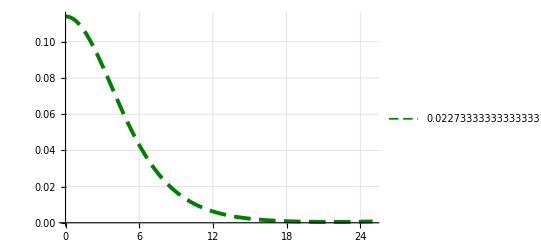

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; (*φ*)

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

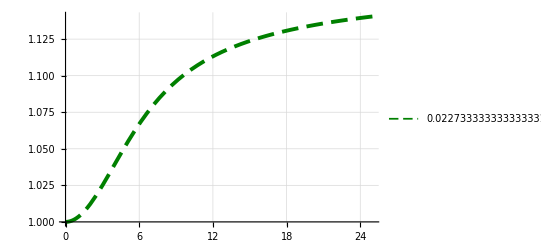

```mathematica
Plot[{Evaluate[NN[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

```mathematica
φ[2.5]/.s
```

{0.165778}

#### Example

```mathematica
AA={0.0227333333333333310888324518828085274435579776763916015625`30.,1.0851212609390880297287722869685471972013459277787175118159`30.,25,30,0.3,0.01`30.};
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;m=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec]*√(8π);
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
c4=-1/2;
L3=(1/η)^(1/3);
p0=0;
ρC=0;
rmax=.

s=NDSolve[{EqsList[[1]],BCList[[1]]},CoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
rmax
```

rmax

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; (*φ*)

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

-Graphics-

```mathematica
Plot[{Evaluate[NN[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

-Graphics-

```mathematica
φ[2.5]/.s
```

{0.165778}